```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\soothair_g09\mindprojects\eigenvalue

### Single CSE, Single Pressure

```mathematica
EigenDataFull=Import["eval.txt","Data"]
```

{{2000,0.001,1.21808×10^7,0.0892075,2.89136×10^-11,6.43929×10^-15},{10000,0.001,2.98869×10^6,0.146767,0.0054473,0.0574625},{15000,0.001,2.25815×10^6,0.312783,0.0384501,0.32316},{18000,0.001,2.00059×10^6,0.427393,0.0739894,0.495524},{20000,0.001,1.86683×10^6,0.505622,0.10372,0.593242},{25000,0.001,1.614×10^6,0.689676,0.202804,0.776188},{28000,0.001,1.49941×10^6,0.787252,0.271688,0.843412},{30000,0.001,1.43373×10^6,0.832001,0.327674,0.880904},{35000,0.001,1.29725×10^6,0.946654,0.462997,0.935204},{40000,0.001,1.18959×10^6,0.990479,0.607405,0.966723}}

```mathematica
Temp=EigenDataFull⟦All,1⟧
```

{2000,10000,15000,18000,20000,25000,28000,30000,35000,40000}

```mathematica
MinRelax=EigenDataFull⟦All,3⟧*EigenDataFull⟦All,4⟧
```

{1.08662×10^6,438641.,706311.,855038.,943910.,1.11314×10^6,1.18041×10^6,1.19286×10^6,1.22805×10^6,1.17826×10^6}

```mathematica
CSE=EigenDataFull⟦All,3⟧*EigenDataFull⟦All,5⟧
```

{0.000352191,16280.3,86826.1,148022.,193628.,327326.,407372.,469796.,600623.,722563.}

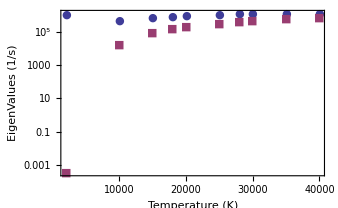

```mathematica
plotframedGT={{Style["EigenValues (1/s)",Italic,17],},{Style[" Temperature (K)",Italic,17],}};
ListLogPlot[{Table[{Temp⟦i⟧,MinRelax⟦i⟧},{i,1,Length[Temp]}],Table[{Temp⟦i⟧,CSE⟦i⟧},{i,1,Length[Temp]}]},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium},
                  PlotRange -> All
                    ]
```

### Multi CSE, Single Pressure

```mathematica
EigenDataFull=Import["eval.txt","Data"]
Temp=EigenDataFull⟦All,1⟧
MinRelax=EigenDataFull⟦All,3⟧*EigenDataFull⟦All,4⟧
```

{{2000,0.001,1.21808×10^7,0.0892075,2.89136×10^-11,6.43929×10^-15},{10000,0.001,2.98869×10^6,0.146767,0.0054473,0.0574625},{15000,0.001,2.25815×10^6,0.312783,0.0384501,0.32316},{18000,0.001,2.00059×10^6,0.427393,0.0739894,0.495524},{20000,0.001,1.86683×10^6,0.505622,0.10372,0.593242},{25000,0.001,1.614×10^6,0.689676,0.202804,0.776188},{28000,0.001,1.49941×10^6,0.787252,0.271688,0.843412},{30000,0.001,1.43373×10^6,0.832001,0.327674,0.880904},{35000,0.001,1.29725×10^6,0.946654,0.462997,0.935204},{40000,0.001,1.18959×10^6,0.990479,0.607405,0.966723}}

{2000,10000,15000,18000,20000,25000,28000,30000,35000,40000}

{1.08662×10^6,438641.,706311.,855038.,943910.,1.11314×10^6,1.18041×10^6,1.19286×10^6,1.22805×10^6,1.17826×10^6}

```mathematica
CSE=Table[0,{i,(Length[EigenDataFull⟦1⟧]-4)/2},{j,Length[Temp]}]
```

{{0,0,0,0,0,0,0,0,0,0}}

```mathematica
For[  i=1,i<(Length[EigenDataFull⟦1⟧]-4)/2+1,i++, CSE⟦i⟧=EigenDataFull⟦All,3⟧*EigenDataFull⟦All,4+2*i-1⟧];
CSE
```

{{0.000352191,16280.3,86826.1,148022.,193628.,327326.,407372.,469796.,600623.,722563.}}

```mathematica
MinRelaxTemp=Table[{Temp⟦i⟧,MinRelax⟦i⟧},{i,1,Length[Temp]}]
```

{{2000,1.08662×10^6},{10000,438641.},{15000,706311.},{18000,855038.},{20000,943910.},{25000,1.11314×10^6},{28000,1.18041×10^6},{30000,1.19286×10^6},{35000,1.22805×10^6},{40000,1.17826×10^6}}

```mathematica
CSETemp=Table[{Temp⟦j⟧,CSE⟦i,j⟧},{i,(Length[EigenDataFull⟦1⟧]-4)/2},{j,Length[Temp]}]
```

{{{2000,0.000352191},{10000,16280.3},{15000,86826.1},{18000,148022.},{20000,193628.},{25000,327326.},{28000,407372.},{30000,469796.},{35000,600623.},{40000,722563.}}}

```mathematica
CSETemp
```

{{{2000,0.000352191},{10000,16280.3},{15000,86826.1},{18000,148022.},{20000,193628.},{25000,327326.},{28000,407372.},{30000,469796.},{35000,600623.},{40000,722563.}}}

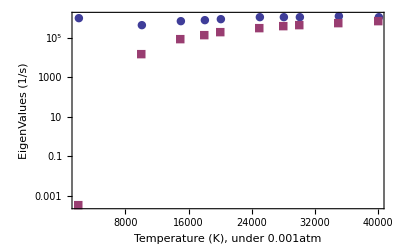

```mathematica
plotframedGT={{Style["EigenValues (1/s)",Italic,17],},{Style[" Temperature (K), under "  <>ToString[EigenDataFull⟦1,2⟧]<>"atm",Italic,17],}};
ListLogPlot[{MinRelaxTemp,CSETemp},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium},
                  PlotRange -> All
                    ]
```

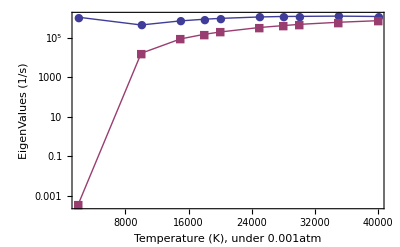

```mathematica
plotframedGT={{Style["EigenValues (1/s)",Italic,17],},{Style[" Temperature (K), under "  <>ToString[EigenDataFull⟦1,2⟧]<>"atm",Italic,17],}};
ListLogPlot[{MinRelaxTemp,CSETemp},
                   Frame-> {{True,True},{True,True}},FrameLabel->plotframedGT,
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium},
                  PlotRange -> All,
                  Joined-> True, InterpolationOrder-> 1
                    ]
```

### Multi CSE, Multi Pressure

```mathematica
PresNum=2;TempNum=10;
EigenDataFull=Import["eval2.txt","Data"]
Temp=EigenDataFull⟦1;;Length[EigenDataFull];;PresNum,1⟧
PresEigenData=Table[0,{i,PresNum},{j,TempNum},{k,Length[EigenDataFull⟦1⟧]}]
For[ i=1,i<PresNum+1,i++,PresEigenData⟦i⟧=Sort[EigenDataFull,#1[[2]]<#2[[2]]&]⟦(i-1)*TempNum+1;;i*TempNum⟧]
PresEigenData
MinRelax=Table[0,{i,PresNum},{j,TempNum}]
For[ i=1,i<PresNum+1,i++,MinRelax⟦i⟧=PresEigenData⟦i,All,3⟧*PresEigenData⟦i,All,4⟧ ]
MinRelaxTemp=Table[0,{i,PresNum},{j,TempNum}]
For[ i =1,i<PresNum+1,i++, {For [j=1,j<TempNum+1,j++ , MinRelaxTemp⟦i,j⟧={PresEigenData⟦i,j,1⟧,MinRelax⟦i,j⟧}]}]
MinRelaxTemp
CSE=Table[0,{k,PresNum},{i,(Length[EigenDataFull⟦1⟧]-4)/2},{j,Length[Temp]}]
For[ i =1,i<PresNum+1,i++, {For [j=1,j<(Length[EigenDataFull⟦1⟧]-4)/2+1,j++ , CSE⟦i,j⟧=PresEigenData⟦i,All,3⟧*PresEigenData⟦i,All,4+2*j-1⟧]}]
CSE
CSETemp=Table[0,{k,PresNum},{i,(Length[EigenDataFull⟦1⟧]-4)/2},{j,Length[Temp]}]
For[ i =1,i<PresNum+1,i++, {For [j=1,j<(Length[EigenDataFull⟦1⟧]-4)/2+1,j++ , { For[k=1,k<TempNum+1,k++,CSETemp⟦i,j,k⟧={PresEigenData⟦i,k,1⟧,CSE⟦i,j,k⟧}]}]}]
CSETemp
Pres=EigenDataFull⟦1;;PresNum,2⟧
```

{{200,0.001,1.21808×10^7,0.0892075,2.89136×10^-11,6.43929×10^-15},{200,1,1.21808×10^10,0.0891713,2.89143×10^-14,-4.44089×10^-16},{400,0.001,6.18774×10^6,0.0724682,4.50332×10^-7,9.03525×10^-7},{400,1,6.18774×10^9,0.0696969,9.7826×10^-10,7.36532×10^-10},{600,0.001,4.39527×10^6,0.0776094,0.0000908584,0.000581555},{600,1,4.39527×10^9,0.0637103,1.61119×10^-6,7.77618×10^-6},{800,0.001,3.51917×10^6,0.102802,0.00122443,0.0116212},{800,1,3.51917×10^9,0.0690069,0.0000793261,0.000667075},{1000,0.001,2.98869×10^6,0.146767,0.0054473,0.0574625},{1000,1,2.98869×10^9,0.0861474,0.000730853,0.00806659},{1200,0.001,2.62866×10^6,0.203052,0.0140642,0.143906},{1200,1,2.62866×10^9,0.113045,0.00287084,0.035391},{1400,0.001,2.36554×10^6,0.276882,0.0292608,0.262841},{1400,1,2.36554×10^9,0.152606,0.00762053,0.093162},{1600,0.001,2.16286×10^6,0.347904,0.0484066,0.381211},{1600,1,2.16286×10^9,0.195386,0.0149734,0.17315},{1800,0.001,2.00059×10^6,0.427393,0.0739894,0.495524},{1800,1,2.00059×10^9,0.246482,0.0256797,0.26843},{2000,0.001,1.86683×10^6,0.505622,0.10372,0.593242},{2000,1,1.86683×10^9,0.300828,0.0393697,0.366208}}

{200,400,600,800,1000,1200,1400,1600,1800,2000}

{{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}},{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}}

{{{2000,0.001,1.86683×10^6,0.505622,0.10372,0.593242},{1800,0.001,2.00059×10^6,0.427393,0.0739894,0.495524},{1600,0.001,2.16286×10^6,0.347904,0.0484066,0.381211},{1400,0.001,2.36554×10^6,0.276882,0.0292608,0.262841},{1200,0.001,2.62866×10^6,0.203052,0.0140642,0.143906},{1000,0.001,2.98869×10^6,0.146767,0.0054473,0.0574625},{800,0.001,3.51917×10^6,0.102802,0.00122443,0.0116212},{600,0.001,4.39527×10^6,0.0776094,0.0000908584,0.000581555},{400,0.001,6.18774×10^6,0.0724682,4.50332×10^-7,9.03525×10^-7},{200,0.001,1.21808×10^7,0.0892075,2.89136×10^-11,6.43929×10^-15}},{{2000,1,1.86683×10^9,0.300828,0.0393697,0.366208},{1800,1,2.00059×10^9,0.246482,0.0256797,0.26843},{1600,1,2.16286×10^9,0.195386,0.0149734,0.17315},{1400,1,2.36554×10^9,0.152606,0.00762053,0.093162},{1200,1,2.62866×10^9,0.113045,0.00287084,0.035391},{1000,1,2.98869×10^9,0.0861474,0.000730853,0.00806659},{800,1,3.51917×10^9,0.0690069,0.0000793261,0.000667075},{600,1,4.39527×10^9,0.0637103,1.61119×10^-6,7.77618×10^-6},{400,1,6.18774×10^9,0.0696969,9.7826×10^-10,7.36532×10^-10},{200,1,1.21808×10^10,0.0891713,2.89143×10^-14,-4.44089×10^-16}}}

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

{{{2000,943910.},{1800,855038.},{1600,752468.},{1400,654975.},{1200,533755.},{1000,438641.},{800,361778.},{600,341114.},{400,448414.},{200,1.08662×10^6}},{{2000,5.61595×10^8},{1800,4.93109×10^8},{1600,4.22593×10^8},{1400,3.60996×10^8},{1200,2.97157×10^8},{1000,2.57468×10^8},{800,2.42847×10^8},{600,2.80024×10^8},{400,4.31266×10^8},{200,1.08618×10^9}}}

{{{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0}}}

{{{193628.,148022.,104697.,69217.6,36970.,16280.3,4308.98,399.347,2.78654,0.000352191}},{{7.34965×10^7,5.13746×10^7,3.23854×10^7,1.80267×10^7,7.54646×10^6,2.18429×10^6,279162.,7081.62,6.05322,0.000352199}}}

{{{0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0}}}

{{{{2000,193628.},{1800,148022.},{1600,104697.},{1400,69217.6},{1200,36970.},{1000,16280.3},{800,4308.98},{600,399.347},{400,2.78654},{200,0.000352191}}},{{{2000,7.34965×10^7},{1800,5.13746×10^7},{1600,3.23854×10^7},{1400,1.80267×10^7},{1200,7.54646×10^6},{1000,2.18429×10^6},{800,279162.},{600,7081.62},{400,6.05322},{200,0.000352199}}}}

{0.001,1}

```mathematica
For[i=1,i<PresNum+1,i++,
aa⟦i⟧=ListLogPlot[{MinRelaxTemp⟦i⟧,CSETemp⟦i⟧},
                   Frame-> {{True,True},{True,True}},
                   FrameLabel->{{Style["EigenValues (1/s)",Italic,17],},{Style[" Temperature (K), under "  <>ToString[Pres⟦i⟧]<>"atm",Italic,17],}},
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium},
                  PlotRange -> All
                    ]
]
```

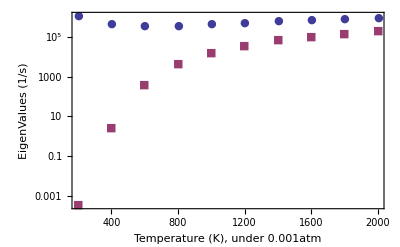

```mathematica
Show[aa⟦1⟧]
```

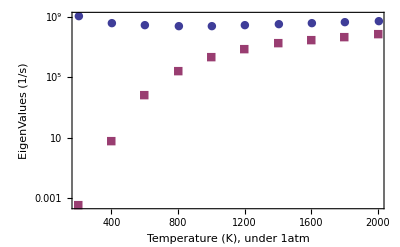

```mathematica
Show[aa⟦2⟧]
```

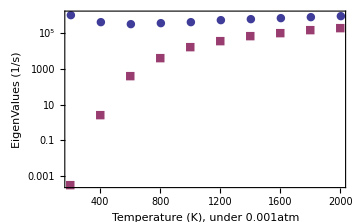
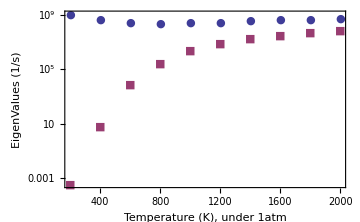

```mathematica
aaa=Table[ListLogPlot[{MinRelaxTemp⟦i⟧,CSETemp⟦i⟧},
                   Frame-> {{True,True},{True,True}},
                   FrameLabel->{{Style["EigenValues (1/s)",Italic,17],},{Style[" Temperature (K), under "  <>ToString[Pres⟦i⟧]<>"atm",Italic,17],}},
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->{White,Dashed},
                  PlotMarkers-> {Automatic,Medium},
                  PlotRange -> All,
                    ImageSize-> Medium],
               {i,PresNum}]
```